#### misc

```mathematica
Clear[r,p,θ,z];
Assuming[{θ∈Reals,r∈Reals,r≥0,Cos[θ]≥0},Integrate[(p^3 Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,-∞,0}]]//Simplify
```

ConditionalExpression[1/(2 (z-Conjugate[z]))ⅈ (-ⅈ √π z MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 z Cos[θ]^2]+π z Sign[r Cos[θ]] (Cosh[r/(√(Sec[θ]^2/z))]-Sinh[r/(√(Sec[θ]^2/z))])+Conjugate[z] (ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[z] Cos[θ]^2]+π Sign[r Cos[θ]] (-Cosh[r/(√(Sec[θ]^2/Conjugate[z]))]+Sinh[r/(√(Sec[θ]^2/Conjugate[z]))]))),(Im[z]≠0&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0)]

```mathematica
Clear[r,p,θ,z];
Assuming[{θ∈Reals,r∈Reals,r≥0,Cos[θ]≥0},Integrate[(p^3 Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//Simplify
```

ConditionalExpression[1/(2 (z-Conjugate[z]))ⅈ (ⅈ √π z MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 z Cos[θ]^2]+π z Sign[r Cos[θ]] (Cosh[r/(√(Sec[θ]^2/z))]-Sinh[r/(√(Sec[θ]^2/z))])+Conjugate[z] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[z] Cos[θ]^2]+π Sign[r Cos[θ]] (-Cosh[r/(√(Sec[θ]^2/Conjugate[z]))]+Sinh[r/(√(Sec[θ]^2/Conjugate[z]))]))),(Im[z]≠0&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0)]

```mathematica
1/(2 (z-Conjugate[z]))ⅈ (ⅈ √π z MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 z Cos[θ]^2]+π z Sign[r Cos[θ]] (Cosh[r/(√(Sec[θ]^2/z))]-Sinh[r/(√(Sec[θ]^2/z))])+Conjugate[z] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[z] Cos[θ]^2]+π Sign[r Cos[θ]] (-Cosh[r/(√(Sec[θ]^2/Conjugate[z]))]+Sinh[r/(√(Sec[θ]^2/Conjugate[z]))])))-1/(2 (z-Conjugate[z]))ⅈ (-ⅈ √π z MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 z Cos[θ]^2]+π z Sign[r Cos[θ]] (Cosh[r/(√(Sec[θ]^2/z))]-Sinh[r/(√(Sec[θ]^2/z))])+Conjugate[z] (ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[z] Cos[θ]^2]+π Sign[r Cos[θ]] (-Cosh[r/(√(Sec[θ]^2/Conjugate[z]))]+Sinh[r/(√(Sec[θ]^2/Conjugate[z]))])))//FullSimplify
```

(√π (-z MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 z Cos[θ]^2]+Conjugate[z] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[z] Cos[θ]^2]))/(z-Conjugate[z])

#### Definitions

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
```

#### String potential (1)

```mathematica
ImVsparcheck1[r_,mD_,v_]:=(2π)/(2π)^3 mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}];
```

```mathematica
ImVsparres1[r_,mD_,v_]:=(2π)/(2π)^3 mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))ⅈ/Im[Πpar[θ,v,mD]](Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]),{θ,0,π/2}]
```

```mathematica
ImVsparcheck1[5,0.15,0.9]
```

0.0038213-2.451×10^-15 ⅈ

```mathematica
ImVsparres1[5,0.15,0.9]
```

0.0038213+5.23665×10^-20 ⅈ

#### String potential (2)

```mathematica
ImVsparcheck2[r_,mD_,v_]:=(2π)/(2π)^3 (1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(p^3 Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}];
```

```mathematica
ImVsparres2[r_,mD_,v_]:=(2π)/(2π)^3(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(√π (Conjugate[Πpar[θ,v,mD]] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[θ,v,mD]] Cos[θ]^2]-Πpar[θ,v,mD] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]))/(2ⅈ Im[Πpar[θ,v,mD]]),{θ,0,π/2-1/1000000},Method->"GlobalAdaptive",WorkingPrecision->10];
```

```mathematica
res[ϵ_]:=(2π)/(2π)^3(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))Re[(√π (Conjugate[Πpar[θ,v,mD]] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[θ,v,mD]] Cos[θ]^2]-Πpar[θ,v,mD] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]))/(2ⅈ Im[Πpar[θ,v,mD]])],{θ,0,π/2-ϵ},Method->"GlobalAdaptive",WorkingPrecision->15];
```

```mathematica
ImVsparcheck2[5,0.15,0.5]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,θ} = {9.35671×10^10,1.5708}. NIntegrate obtained 1.10019+2.85581×10^-10 ⅈ and 0.00017326 for the integral and error estimates.

0.018101+4.69852×10^-12 ⅈ

```mathematica
ImVsparres2[5,0.15,0.5]
```

0.0181004+3.19298×10^-6 ⅈ

#### String potential

```mathematica
g[r_,mD_,v_]:=(1-v^2)^(3/2)(NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(ⅈ mD^2)/Im[Πpar[θ,v,mD]](Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]),{θ,0,π/2}]+NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(√π (Conjugate[Πpar[θ,v,mD]] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[θ,v,mD]] Cos[θ]^2]-Πpar[θ,v,mD] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]))/(2ⅈ Im[Πpar[θ,v,mD]]),{θ,0,π/2-1/1000000}]);
```

```mathematica
4 π^2(ImVsparcheck1[5,0.15,0.01]+ImVsparcheck2[5,0.15,0.01])
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,θ} = {9.35671×10^10,1.5708}. NIntegrate obtained 0.935412-3.16049×10^-11 ⅈ and 0.0000755588 for the integral and error estimates.

1.72045-9.77051×10^-10 ⅈ

```mathematica
g[5,0.15,0.01]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707891938680112609157905195766957717751211021095514297485351563}. NIntegrate obtained 0.935386-0.000078354 ⅈ and 0.0009836 for the integral and error estimates.

1.72042-0.0000783423 ⅈ

```mathematica
gold[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
```

```mathematica
gold[5 0.15]
```

1.72107

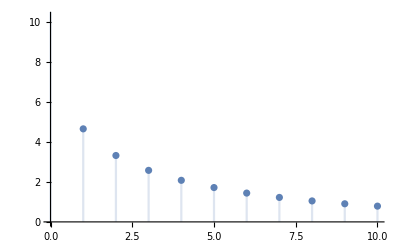

```mathematica
DiscretePlot[gold[r 0.15],{r,0,10,1}]
```